```mathematica
(*First we curve-fit Pfail as a function of p and L, in accordance with (A1) of Watson and Barrett (2014)*)
SetDirectory[NotebookDirectory[]];
s=Import["results_Toric.xlsx"][[1]];
sNames=s[[1]]
sData=s[[2;;]]
sData[[;;,1]]
```

{p,L,I,varI}

{{0.01,3.,0.00607114,3.01409×10^-6},{0.01,4.,0.0203482,5.42996×10^-6},{0.01,5.,0.00101372,8.52415×10^-6},{0.01,6.,0.00210683,0.0000122406},{0.01,7.,0.000126092,0.0000166241},{0.01,8.,0.000172583,0.0000220692},{0.01,9.,0.0000296,0.0000303601},{0.01,10.,0.0000237,0.000050127},{0.01,11.,2.86×10^-6,0.000124379},{0.02,3.,0.0194696,4.03636×10^-6},{0.02,4.,0.0614899,7.41227×10^-6},{0.02,5.,0.00683277,0.0000119909},{0.02,6.,0.0135489,0.0000194487},{0.02,7.,0.00277565,0.0000254431},{0.02,8.,0.00338513,0.0000827259},{0.02,9.,0.000540757,0.000178652},{0.02,10.,0.000608776,0.0000618093},{0.02,11.,0.000100915,0.0000860797},{0.03,3.,0.0370544,4.44638×10^-6},{0.03,4.,0.112207,8.30863×10^-6},{0.03,5.,0.020907,0.0000136111},{0.03,6.,0.044175,0.0000243027},{0.03,7.,0.0121366,0.000090667},{0.03,8.,0.0179061,0.000506752},{0.03,9.,0.00501285,0.0000964873},{0.03,10.,0.00549873,0.000142701},{0.03,11.,0.00151189,0.0002887},{0.04,3.,0.0573045,4.50062×10^-6},{0.04,4.,0.1616,8.51239×10^-6},{0.04,5.,0.0411101,0.0000146179},{0.04,6.,0.112295,0.000020653},{0.04,7.,0.0392878,0.000254794},{0.04,8.,0.0573678,0.0000951196},{0.04,9.,0.0227223,0.000126377},{0.04,10.,0.0248488,},{0.04,11.,0.00977385,},{0.05,3.,0.07725,4.32911×10^-6},{0.05,4.,0.204878,8.25737×10^-6},{0.05,5.,0.0580166,0.0000153692},{0.05,6.,0.101714,0.0000370756},{0.05,7.,0.114961,0.0000550454},{0.05,8.,0.132664,0.000148927},{0.05,9.,0.0681931,0.000232207},{0.05,10.,0.0738913,},{0.05,11.,0.0381862,},{0.06,3.,0.0953875,4.01047×10^-6},{0.06,4.,0.238538,7.6894×10^-6},{0.06,5.,0.065912,0.0000156803},{0.06,6.,0.186364,0.000107586},{0.06,7.,0.21547,0.0000811079},{0.06,8.,0.246046,0.000322473},{0.06,9.,0.154268,},{0.06,10.,0.16728,},{0.06,11.,0.106037,}}

{0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.01,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.02,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.04,0.04,0.04,0.04,0.04,0.04,0.04,0.04,0.04,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.05,0.06,0.06,0.06,0.06,0.06,0.06,0.06,0.06,0.06}

{{{3.,0.00610.0035},{4.,0.0200.005},{5.,0.0010.006},{6.,0.0020.007},{7.,0.0000.008},{8.,0.0000.009},{9.,0.0000.011},{10.,0.0000.014},{11.,0.0000.022}},{{3.,0.0190.004},{4.,0.0610.005},{5.,0.0070.007},{6.,0.0140.009},{7.,0.0030.010},{8.,0.0030.018},{9.,0.0000.027},{10.,0.0000.016},{11.,0.0000.019}},{{3.,0.0370.004},{4.,0.1120.006},{5.,0.0210.007},{6.,0.0440.010},{7.,0.0120.019},{8.,0.020.05},{9.,0.0050.020},{10.,0.0050.024},{11.,0.0020.034}},{{3.,0.0570.004},{4.,0.1620.006},{5.,0.0410.008},{6.,0.1120.009},{7.,0.0390.032},{8.,0.0570.020},{9.,0.0230.022},{10.,0.02484882 √},{11.,0.009773852 √}},{{3.,0.0770.004},{4.,0.2050.006},{5.,0.0580.008},{6.,0.1020.012},{7.,0.1150.015},{8.,0.1330.024},{9.,0.0680.030},{10.,0.07389132 √},{11.,0.03818622 √}},{{3.,0.0950.004},{4.,0.2390.006},{5.,0.0660.008},{6.,0.1860.021},{7.,0.2150.018},{8.,0.250.04},{9.,0.1542682 √},{10.,0.167282 √},{11.,0.1060372 √}}}

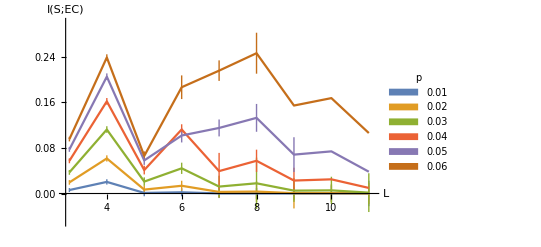

file.pdf

```mathematica
Transpose[{sData[[;;,3]],2*Sqrt[sData[[;;,3]]]}];
Data=Apply[Around,Transpose[{sData[[;;,3]],2*Sqrt[sData[[;;,4]]]}],1];
DataPlot=Partition[Transpose[{sData[[;;,2]],Data}],9]
plot=ListLinePlot[DataPlot,AxesLabel->{"L","I(S;EC)"},PlotRange->{{2.9,11.1},{-0.05,0.3}},PlotLegends->Placed[SwatchLegend[DeleteDuplicates[sData[[;;,1]]],LegendLabel->"p"],Automatic]]
Export["file.pdf",plot]
```